```mathematica
Clear[ProgressMap]
ProgressMap=ResourceFunction["DynamicMap"]
```

```mathematica
MinimalBooleanForm[bf_]:=First[MinimalBy[Join[First[BooleanMinimize[bf, #]]&/@{"DNF","CNF","ANF", "NOR", "NAND","AND", "OR"}, FullSimplify[First[BooleanConvert[bf, #]]]&/@{"ESOP", "NOR2", "NAND2", "BDT"}], VertexCount@*ExpressionTree]]
```

```mathematica
MinimalBooleanForm[BooleanFunction[…]]
(VertexCount@*ExpressionTree)[%]
```

((#1&&#2)⊻(#1&&#3)⊻(#1&&#4)⊻(#1&&#5))||(!#1&&((#3&&#2)⊻(#4&&#2)⊻(#4&&#3)⊻(#4&&#5)⊻(#5&&#2)⊻(#5&&#3)⊻(#4&&#3&&#2)⊻(#4&&#5&&#2)⊻(#4&&#5&&#3)⊻(#5&&#3&&#2)⊻(#4&&#5&&#3&&#2)))

94

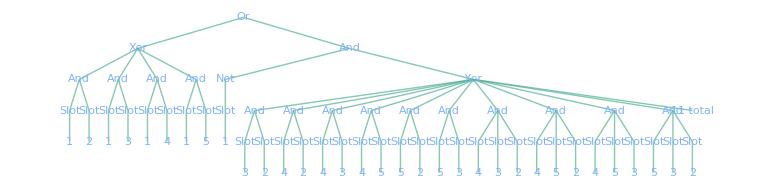

```mathematica
ExpressionTree[(((#1&&#2)⊻(#1&&#3)⊻(#1&&#4)⊻(#1&&#5))||(!#1&&((#3&&#2)⊻(#4&&#2)⊻(#4&&#3)⊻(#4&&#5)⊻(#5&&#2)⊻(#5&&#3)⊻(#4&&#3&&#2)⊻(#4&&#5&&#2)⊻(#4&&#5&&#3)⊻(#5&&#3&&#2)⊻(#4&&#5&&#3&&#2))))]
```

```mathematica
MultiwaySystem=ResourceFunction["MultiwaySystem"];
```

```mathematica
Thing[depth_]:=If[depth==0,{a[1],a[2], a[3],a[4], a[5], False, True},ParallelMap[FullSimplify,Union[With[{res=Thing[depth-1]}, Join[res,Table[Not[result], {result, res}], Join@@Table[And[res[[i]], res[[j]]], {i, Length[res]}, {j, i-1}], Join@@Table[Or[res[[i]], res[[j]]], {i, Length[res]}, {j, i-1}], Join@@Table[Xor[res[[i]], res[[j]]], {i, Length[res]}, {j, i-1}]]]]]]
```

```mathematica
Thing[1]
```

{False,True,a[1],a[2],a[3],a[4],a[5],a[2]&&a[1],a[3]&&a[1],a[3]&&a[2],a[4]&&a[1],a[4]&&a[2],a[4]&&a[3],a[5]&&a[1],a[5]&&a[2],a[5]&&a[3],a[5]&&a[4],!a[1],!a[2],!a[3],!a[4],!a[5],a[2]||a[1],a[3]||a[1],a[3]||a[2],a[4]||a[1],a[4]||a[2],a[4]||a[3],a[5]||a[1],a[5]||a[2],a[5]||a[3],a[5]||a[4],a[1]⊻a[2],a[1]⊻a[3],a[1]⊻a[4],a[1]⊻a[5],a[2]⊻a[3],a[2]⊻a[4],a[2]⊻a[5],a[3]⊻a[4],a[3]⊻a[5],a[4]⊻a[5]}

```mathematica
BoolExprNumber[expr_]:=FromDigits[Table[Boole[expr/.Thread[(a/@Range[5])->Positive[IntegerDigits[num, 2, 5]]]], {num, 0, 2^5-1}], 2]
```

```mathematica
last={a[1],a[2], a[3],a[4], a[5], False, True}

next=Association[BoolExprNumber[#]->#&/@last]

res=Values[next]

last=Join[res,Table[Not[result], {result, res}], Join@@Table[And[res[[i]], res[[j]]], {i, Length[res]}, {j, i-1}], Join@@Table[Or[res[[i]], res[[j]]], {i, Length[res]}, {j, i-1}], Join@@Table[Xor[res[[i]], res[[j]]], {i, Length[res]}, {j, i-1}]]

next=Association[BoolExprNumber[#]->#&/@last]

res=Values[next]

last=Join[res,Table[Not[result], {result, res}], Join@@Table[And[res[[i]], res[[j]]], {i, Length[res]}, {j, i-1}], Join@@Table[Or[res[[i]], res[[j]]], {i, Length[res]}, {j, i-1}], Join@@Table[Xor[res[[i]], res[[j]]], {i, Length[res]}, {j, i-1}]]

next=Association[BoolExprNumber[#]->#&/@last]

res=Values[next]
```

{a[1],a[2],a[3],a[4],a[5],False,True}

<|65535→a[1],16711935→a[2],252645135→a[3],858993459→a[4],1431655765→a[5],0→False,4294967295→True|>

{a[1],a[2],a[3],a[4],a[5],False,True}

{a[1],a[2],a[3],a[4],a[5],False,True,!a[1],!a[2],!a[3],!a[4],!a[5],True,False,a[2]&&a[1],a[3]&&a[1],a[3]&&a[2],a[4]&&a[1],a[4]&&a[2],a[4]&&a[3],a[5]&&a[1],a[5]&&a[2],a[5]&&a[3],a[5]&&a[4],False,False,False,False,False,a[1],a[2],a[3],a[4],a[5],False,a[2]||a[1],a[3]||a[1],a[3]||a[2],a[4]||a[1],a[4]||a[2],a[4]||a[3],a[5]||a[1],a[5]||a[2],a[5]||a[3],a[5]||a[4],a[1],a[2],a[3],a[4],a[5],True,True,True,True,True,True,a[1]⊻a[2],a[1]⊻a[3],a[2]⊻a[3],a[1]⊻a[4],a[2]⊻a[4],a[3]⊻a[4],a[1]⊻a[5],a[2]⊻a[5],a[3]⊻a[5],a[4]⊻a[5],a[1],a[2],a[3],a[4],a[5],!a[1],!a[2],!a[3],!a[4],!a[5],True}

<|65535→a[1],16711935→a[2],252645135→a[3],858993459→a[4],1431655765→a[5],0→False,4294967295→True,4294901760→!a[1],4278255360→!a[2],4042322160→!a[3],3435973836→!a[4],2863311530→!a[5],255→a[2]&&a[1],3855→a[3]&&a[1],983055→a[3]&&a[2],13107→a[4]&&a[1],3342387→a[4]&&a[2],50529027→a[4]&&a[3],21845→a[5]&&a[1],5570645→a[5]&&a[2],84215045→a[5]&&a[3],286331153→a[5]&&a[4],16777215→a[2]||a[1],252706815→a[3]||a[1],268374015→a[3]||a[2],859045887→a[4]||a[1],872363007→a[4]||a[2],1061109567→a[4]||a[3],1431699455→a[5]||a[1],1442797055→a[5]||a[2],1600085855→a[5]||a[3],2004318071→a[5]||a[4],16776960→a[1]⊻a[2],252702960→a[1]⊻a[3],267390960→a[2]⊻a[3],859032780→a[1]⊻a[4],869020620→a[2]⊻a[4],1010580540→a[3]⊻a[4],1431677610→a[1]⊻a[5],1437226410→a[2]⊻a[5],1515870810→a[3]⊻a[5],1717986918→a[4]⊻a[5]|>

{a[1],a[2],a[3],a[4],a[5],False,True,!a[1],!a[2],!a[3],!a[4],!a[5],a[2]&&a[1],a[3]&&a[1],a[3]&&a[2],a[4]&&a[1],a[4]&&a[2],a[4]&&a[3],a[5]&&a[1],a[5]&&a[2],a[5]&&a[3],a[5]&&a[4],a[2]||a[1],a[3]||a[1],a[3]||a[2],a[4]||a[1],a[4]||a[2],a[4]||a[3],a[5]||a[1],a[5]||a[2],a[5]||a[3],a[5]||a[4],a[1]⊻a[2],a[1]⊻a[3],a[2]⊻a[3],a[1]⊻a[4],a[2]⊻a[4],a[3]⊻a[4],a[1]⊻a[5],a[2]⊻a[5],a[3]⊻a[5],a[4]⊻a[5]}

/tmp/m0000041939811

String

```mathematica
CreatePLAFile[numInputs_, bf_]:=TextString[StringForm[".i ``\n.o 1\n.p ``\n", numInputs, 2^numInputs]]<>StringRiffle[Table[IntegerString[i, 2, numInputs]<>" "<>ToString[Boole[bf@@Positive[IntegerDigits[i, 2, numInputs]]]], {i, 0, 2^numInputs-1}], "\n"]<>"\n.e"
```

```mathematica
file=CreateFile[]
WriteString[file, CreatePLAFile[5, BooleanFunction[12534, 5]]]
```

/tmp/m0000071939811

```mathematica
Import["/tmp/m0000071939811"]
```

{{.i,5},{.o,1},{.p,32},{0,0},{1,1},{10,1},{11,0},{100,1},{101,1},{110,1},{111,1},{1000,0},{1001,0},{1010,0},{1011,0},{1100,1},{1101,1},{1110,0},{1111,0},{10000,0},{10001,0},{10010,0},{10011,0},{10100,0},{10101,0},{10110,0},{10111,0},{11000,0},{11001,0},{11010,0},{11011,0},{11100,0},{11101,0},{11110,0},{11111,0},{.e}}

```mathematica
2^(2^5)
```

4294967296

```mathematica
IntegerDigits[4294967296-1, 2]//Length
```

32

```mathematica
FromDigits[IntegerDigits[01100110011001100110011001100110, 10, 32], 2]
```

1717986918

```mathematica
BooleanConvert[BooleanFunction[1717986918], "ANF"]
```

#4⊻#5&

2863311530

3435973836

4042322160

4278255360

4294901760

```mathematica
res=<|av->a, bv->b, cv->c, dv->d, ev->e|>;
```

```mathematica
res=Join[Association[Join[BitXor[#[[1, 1]], #[[2, 1]]]->Xor[#[[1, 2]], #[[2, 2]]]&/@Subsets[Normal[res], {2, 2}],BitOr[#[[1, 1]], #[[2, 1]]]->Or[#[[1, 2]], #[[2, 2]]]&/@Subsets[Normal[res], {2, 2}],BitAnd[#[[1, 1]], #[[2, 1]]]->And[#[[1, 2]], #[[2, 2]]]&/@Subsets[Normal[res], {2, 2}], BitNot[#[[1]]]->Not[#[[2]]]&/@Normal[res], Normal[res]]]]
```

<|BitXor[av,bv]→a⊻b,BitXor[av,cv]→a⊻c,BitXor[av,dv]→a⊻d,BitXor[av,ev]→a⊻e,BitXor[bv,cv]→b⊻c,BitXor[bv,dv]→b⊻d,BitXor[bv,ev]→b⊻e,BitXor[cv,dv]→c⊻d,BitXor[cv,ev]→c⊻e,BitXor[dv,ev]→d⊻e,BitOr[av,bv]→a||b,BitOr[av,cv]→a||c,BitOr[av,dv]→a||d,BitOr[av,ev]→a||e,BitOr[bv,cv]→b||c,BitOr[bv,dv]→b||d,BitOr[bv,ev]→b||e,BitOr[cv,dv]→c||d,BitOr[cv,ev]→c||e,BitOr[dv,ev]→d||e,BitAnd[av,bv]→a&&b,BitAnd[av,cv]→a&&c,BitAnd[av,dv]→a&&d,BitAnd[av,ev]→a&&e,BitAnd[bv,cv]→b&&c,BitAnd[bv,dv]→b&&d,BitAnd[bv,ev]→b&&e,BitAnd[cv,dv]→c&&d,BitAnd[cv,ev]→c&&e,BitAnd[dv,ev]→d&&e,BitNot[av]→!a,BitNot[bv]→!b,BitNot[cv]→!c,BitNot[dv]→!d,BitNot[ev]→!e,av→a,bv→b,cv→c,dv→d,ev→e|>

```mathematica
res=<|av->a, bv->b, cv->c, dv->d|>;

booleanfunctionnumber=120;

While[!KeyExistsQ[res, booleanfunctionnumber],
PrintTemporary["Size is ", ByteCount[res]];
res=Join[Association[Join[
Join@@ProgressMap[{BitXor[#[[1, 1]], #[[2, 1]]]->Xor[#[[1, 2]], #[[2, 2]]], BitOr[#[[1, 1]], #[[2, 1]]]->Or[#[[1, 2]], #[[2, 2]]], BitAnd[#[[1, 1]], #[[2, 1]]]->And[#[[1, 2]], #[[2, 2]]]}&,Subsets[Normal[res], {2, 2}]],

BitNot[#[[1]]]->Not[#[[2]]]&/@Normal[res],
Normal[res]
]]]]

res[booleanfunctionnumber]
BooleanConvert[BooleanFunction[booleanfunctionnumber], "ANF"]
```

```mathematica
{}
```

```mathematica
RandomInteger[2^16]
```

12003

```mathematica
ResourceFunction["BooleanCompose"]
```

```mathematica
BooleanConvert[Xor[Xor[a, b, c, d], Or[a, b, c, d]], "BFF"]
```

BooleanFunction[…][a,b,c,d]

```mathematica
,,,
```

```mathematica
1+1
```

2